```mathematica
SetDirectory["C:\\Users\\griho\\OneDrive\\Рабочий стол\\Численные методы\\Thermal Conductivity\\Программа\\ThermalConductivity"];
```

```mathematica
data=Import["test.txt", "Table"];
l=data[[1,1]];
x=Table[i*l/(Length@data[[2]]-1),{i,0,Length@data[[2]]-1}];
data=Delete[data,1];
Dimensions@data
min=Min[data]
max=Max[data]
posMax=Position[data,max]
```

{2,11}

4.68165

5

{{1,1},{1,11}}

```mathematica
Table[Print@Which[posMax[[i,1]]==1,"Максимум достигается при t=0",posMax[[i,2]]==1,"Максимум достигается на левом конце",posMax[[i,2]]==Length@data[[1]],"Максимум достигается на правом конце",True,"Нарушение монотонности"],{i,Length@posMax}];
```

Максимум достигается при t=0

Максимум достигается при t=0

Эволюция решения на протяжении всего решения

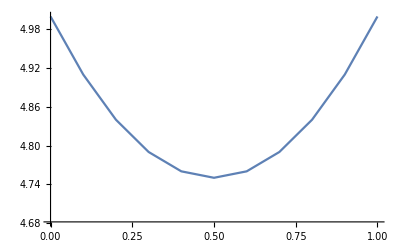

```mathematica
GraphicsGrid@Partition[Map[ListLinePlot[MapIndexed[{el,i}|->{x[[First@i]],el},#],PlotRange->{{0,Last@x},MinMax@data}]&,data[[;;;;50]]],UpTo[3]]
```

```mathematica
Manipulate[ListLinePlot[data[[i]],PlotRange->All],{i,1,20,1}]
```

Эволюция решения в начальные моменты времени

```mathematica
maxTime=10;
GraphicsGrid@Partition[Map[ListLinePlot[MapIndexed[{el,i}|->{x[[First@i]],el},#],PlotRange->{{0,Last@x},MinMax@data[[;;maxTime]]}]&,data[[;;maxTime;;1]]],UpTo[3]]
```

Part::take: Cannot take positions 1 through 10 in {{5,4.91,4.84,4.79,4.76,4.75,4.76,4.79,4.84,4.91,«1»},{4.68165,4.76847,4.83245,4.87629,4.90185,4.91025,4.90185,4.87629,4.83245,4.76847,«1»}}.

General::prng: Value of option PlotRange -> {{0,1},{{{5,4.91,4.84,4.79,4.76,4.75,4.76,4.79,4.84,4.91,«1»},{4.68165,4.76847,4.83245,4.87629,4.90185,4.91025,4.90185,4.87629,4.83245,4.76847,«1»}}⟦1;;10⟧,{{5,4.91,4.84,4.79,4.76,4.75,4.76,4.79,4.84,4.91,«1»},{4.68165,4.76847,4.83245,4.87629,4.90185,4.91025,4.90185,4.87629,4.83245,4.76847,«1»}}⟦1;;10⟧}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Part::take: Cannot take positions 1 through 10 in {{5,4.91,4.84,4.79,4.76,4.75,4.76,4.79,4.84,4.91,«1»},{4.68165,4.76847,4.83245,4.87629,4.90185,4.91025,4.90185,4.87629,4.83245,4.76847,«1»}}.

General::stop: Further output of Part::take will be suppressed during this calculation.

General::prng: Value of option PlotRange -> {{0,1},{{{5,4.91,4.84,4.79,4.76,4.75,4.76,4.79,4.84,4.91,«1»},{4.68165,4.76847,4.83245,4.87629,4.90185,4.91025,4.90185,4.87629,4.83245,4.76847,«1»}}⟦1;;10⟧,{{5,4.91,4.84,4.79,4.76,4.75,4.76,4.79,4.84,4.91,«1»},{4.68165,4.76847,4.83245,4.87629,4.90185,4.91025,4.90185,4.87629,4.83245,4.76847,«1»}}⟦1;;10⟧}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListLinePlot::lpn: {0.,1.};;{0.1,10.};;{0.2,1.} is not a list of numbers or pairs of numbers.

Part::pkspec1: The expression ListLinePlot[{0,1};;{1/10,10};;{1/5,1},PlotRange→{{0,1},{{{5,4.91,4.84,4.79,4.76,4.75,4.76,4.79,4.84,4.91,«1»},{4.68165,4.76847,4.83245,4.87629,4.90185,4.91025,4.90185,4.87629,4.83245,4.76847,«1»}}⟦1;;10⟧,{{5,4.91,4.84,4.79,4.76,4.75,4.76,4.79,4.84,4.91,«1»},{4.68165,4.76847,4.83245,4.87629,4.90185,4.91025,4.90185,4.87629,4.83245,4.76847,«1»}}⟦1;;10⟧}}] cannot be used as a part specification.

GraphicsGrid::list: ()⟦ListLinePlot[{0,1};;{1/10,10};;{1/5,1},PlotRange→{{0,1},{{{«11»},{«11»}}⟦1;;10⟧,{{«11»},{«11»}}⟦1;;10⟧}}]⟧ is not a list of lists.

GraphicsGrid[(-Graphics-)⟦ListLinePlot[{0,1};;{1/10,10};;{1/5,1},PlotRange→{{0,1},{{{5,4.91,4.84,4.79,4.76,4.75,4.76,4.79,4.84,4.91,5},{4.68165,4.76847,4.83245,4.87629,4.90185,4.91025,4.90185,4.87629,4.83245,4.76847,4.68165}}⟦1;;10⟧,{{5,4.91,4.84,4.79,4.76,4.75,4.76,4.79,4.84,4.91,5},{4.68165,4.76847,4.83245,4.87629,4.90185,4.91025,4.90185,4.87629,4.83245,4.76847,4.68165}}⟦1;;10⟧}}]⟧]

```mathematica
ListLinePlot[data[[12]]]
```

Part::partw: Part 12 of {{5,4.91,4.84,4.79,4.76,4.75,4.76,4.79,4.84,4.91,«1»},{4.68165,4.76847,4.83245,4.87629,4.90185,4.91025,4.90185,4.87629,4.83245,4.76847,«1»}} does not exist.

Part::partw: Part 12 of {{5.,4.91,4.84,4.79,4.76,4.75,4.76,4.79,4.84,4.91,«1»},{4.68165,4.76847,4.83245,4.87629,4.90185,4.91025,4.90185,4.87629,4.83245,4.76847,«1»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::pkspec1: The expression False cannot be used as a part specification.

ListLinePlot::lpn: {{5.,4.91,4.84,4.79,4.76,4.75,4.76,4.79,4.84,4.91,«1»},{4.68165,4.76847,4.83245,4.87629,4.90185,4.91025,4.90185,4.87629,4.83245,4.76847,«1»}}⟦12⟧ is not a list of numbers or pairs of numbers.

ListLinePlot[{{5,4.91,4.84,4.79,4.76,4.75,4.76,4.79,4.84,4.91,5},{4.68165,4.76847,4.83245,4.87629,4.90185,4.91025,4.90185,4.87629,4.83245,4.76847,4.68165}}⟦12⟧]

```mathematica
ListPlot3D[data,PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[data,PlotRange->All]
```

-Graphics3D-

```mathematica
A=5;
a=3;
T=10.0;
k=20;
Plot3D[(A x)/l ⅇ^-t+(2A l^2)/π∑_(n=1)^k ((-1)^n(ⅇ^(-((π n)/l)^2 a^2 t)-ⅇ^-t))/(n(n^2 π^2 a^2-l^2))Sin[(n π x)/l],{x,0,l},{t,0,T},PlotRange->All]
```

-Graphics3D-

#### Случай K(u)

```mathematica
data=Import["testU.txt", "Table"];
l=data[[1,1]];
x=Table[i*l/(Length@data[[2]]-1),{i,0,Length@data[[2]]-1}];
data=Delete[data,1];
Dimensions@data
min=Min[data]
max=Max[data]
posMax=Position[data,max]
ListPlot3D[data,PlotRange->All]
```

{5000,51}

0

10

{{5000,1}}

-Graphics3D-

```mathematica
σ=2.0;
κ0=0.5;
c=5;
uExact[x_,t_]:=If[x<=c t,((σ c)/κ0(c t-x))^(1/σ),0]
L=10;
T=1;
Plot3D[uExact[x,t],{x,0,L},{t,0,T},PlotRange->All,AxesLabel->{"x","t"},ExclusionsStyle->Orange]
```

-Graphics3D-

#### График погрешностей для K(u):

h = 0.2:

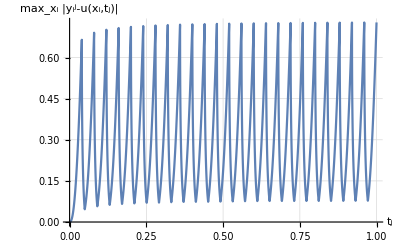

```mathematica
err=Flatten@Import["error.txt","Table"];
τ=err[[1]];
err=Table[{τ(i-2),err[[i]]},{i,2,Length@err}];
ListLinePlot[err,AxesLabel->{"t_j","max_x_i |y_i^j-u(x_i,t_j)|"},GridLines->Automatic]
```

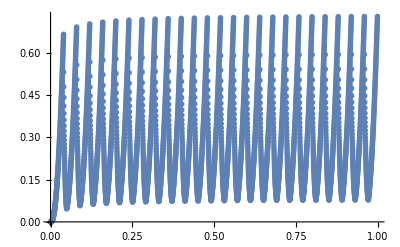

```mathematica
ListLinePlot[err,PlotMarkers->{Red,0.007}]
```

h = 0.05:

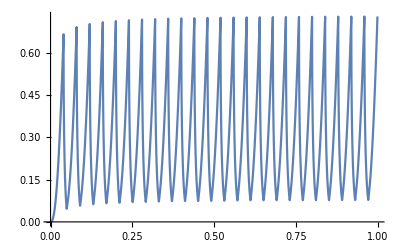

```mathematica
err=Flatten@Import["error.txt","Table"];
τ=err[[1]];
err=Table[{τ(i-2),err[[i]]},{i,2,Length@err}];
ListLinePlot[err]
```

#### Консервативность

σ = 0

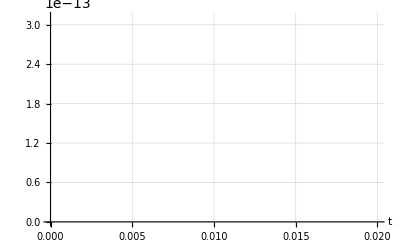

```mathematica
diff=Flatten@Import["cons.txt","Table"];
τ=0.01;
diff=Table[{τ i,diff[[i]]},{i,Length@diff}];
ListLinePlot[diff,GridLines->Automatic,AxesLabel->{"t"}]
```

σ = 0.5

```mathematica
diff=Flatten@Import["cons.txt","Table"];
τ=0.01;
diff=Table[{τ i,diff[[i]]},{i,Length@diff}];
ListLinePlot[diff,GridLines->Automatic,AxesLabel->{"t"}]
```

-Graphics-